```mathematica
FindMPGContraction[g_]:=Block[{i, edges=EdgeList[g],e},
For[i=1,i≤Length[edges],i++,
e=edges[[i]];
If[MaximalPlanarQ[EdgeContract[g,e]],
Return[True]
]
];
Return[False]
]
```

```mathematica
Timing[Fold[And,Monitor[Table[If[!FindMPGContraction[ReadGrof[k]],Print[k];False,True],{k,398438}],k]]]
```

{781.438,True}

```mathematica
Length[plantri]
```

100000

```mathematica
Timing[Fold[And,Monitor[Table[If[!FindMPGContraction[Graph[plantri[[k]]]],Print[k];False,True],{k,100000}],k]]]
```

{825.188,True}

```mathematica
Fold[And,Monitor[Table[If[!FindMPGContraction[Graph[plantri[[k]]]],Print[k];False,True],{k,1000}],k]]
```

True

```mathematica
FindNonMPGContraction[g_]:=Block[{i, edges=EdgeList[g],e, result={}},
For[i=1,i≤Length[edges],i++,
e=edges[[i]];
If[!MaximalPlanarQ[EdgeContract[g,e]],
AppendTo[result,e]
]
];result
]
```

```mathematica
FindNonMPGContraction[ReadGrof[2]]
```

2<->3

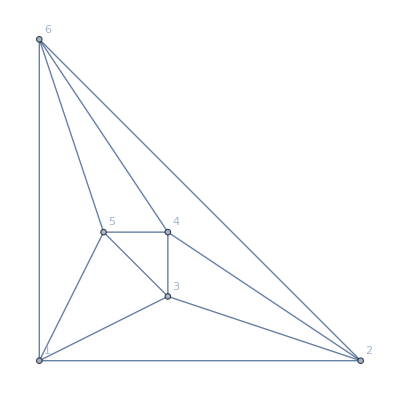
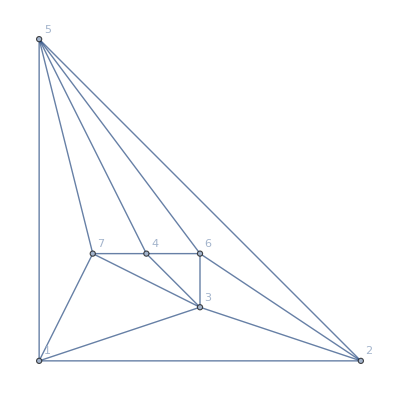
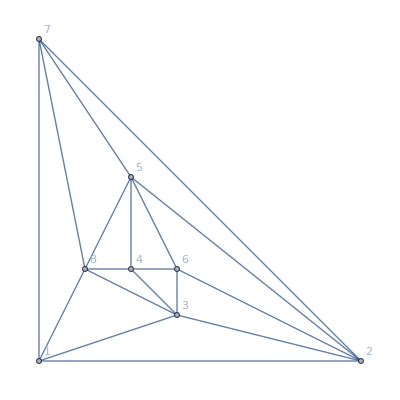
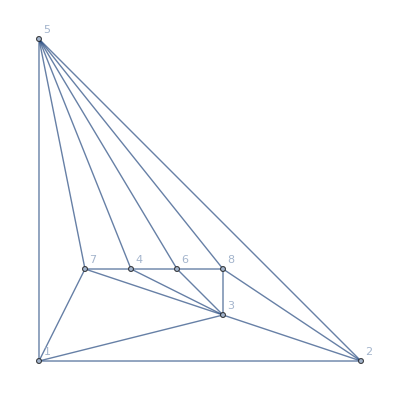
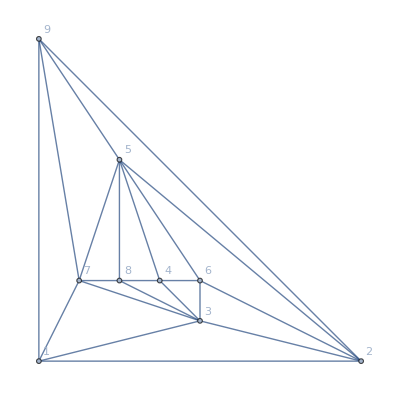
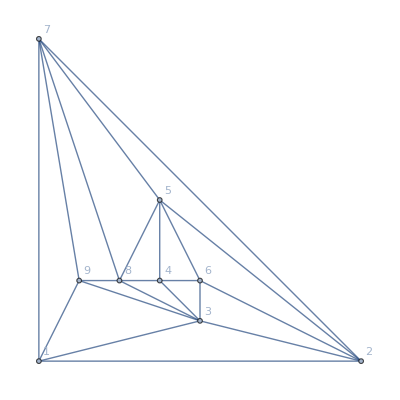
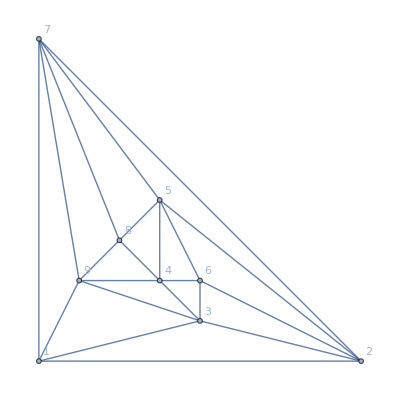
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graph[ReadGrof[k],VertexLabels->"Name", GraphHighlight->FindNonMPGContraction[ReadGrof[k]], GraphLayout->"PlanarEmbedding", GraphHighlightStyle->"Thick"],{k,2,50}]
```

```mathematica
FindMPGContractionEdges[g_]:=Block[{i, edges=EdgeList[g],e, result={},h},
For[i=1,i≤Length[edges],i++,
e=edges[[i]];
h=EdgeContract[g,e];
If[MaximalPlanarQ[h],
AppendTo[result,e->Style[ChromaticPolynomial[EdgeDelete[g,e],4]/24,Darker[Green],Bold]]
]
];result
]
```

```mathematica
Table[With[{g=ReadGrof[k]},With[{lab=FindMPGContractionEdges[g]}, Graph[g,VertexLabels->"Name", GraphHighlight->Map[First,lab],EdgeLabels->lab, GraphLayout->"PlanarEmbedding", GraphHighlightStyle->"Thick"]]],{k,2,30}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[With[{g=JacobsThalGraph[k]},With[{lab=FindMPGContractionEdges[g]}, Graph[g,VertexLabels->"Name", GraphHighlight->Map[First,lab],EdgeLabels->lab, GraphLayout->"PlanarEmbedding", GraphHighlightStyle->"Thick"]]],{k,2,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[With[{g=ReadGrof[k]},With[{lab=FindMPGContractionEdges[g]}, Labeled[Graph[g,VertexLabels->"Name", GraphHighlight->Map[First,lab],EdgeLabels->lab, GraphLayout->"PlanarEmbedding", GraphHighlightStyle->"Thick"],ChromaticPolynomial[g,4]/24]]],{k,2,10}]
```

{-Graphics-1,-Graphics-1,-Graphics-4,-Graphics-1,-Graphics-4,-Graphics-5,-Graphics-1,-Graphics-1,-Graphics-1}

```mathematica
Table[With[{g=MinimalGraph[k]},With[{lab=FindMPGContractionEdges[g]}, Labeled[Graph[g,VertexLabels->"Name", GraphHighlight->Map[First,lab],EdgeLabels->lab, GraphLayout->"PlanarEmbedding", GraphHighlightStyle->"Thick"],ChromaticPolynomial[g,4]/24]]],{k,2,10}]
```

{-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1}

```mathematica
Table[With[{g=MinimalGraph2[k]},With[{lab=FindMPGContractionEdges[g]}, Labeled[Graph[g,VertexLabels->"Name", GraphHighlight->Map[First,lab],EdgeLabels->lab, GraphLayout->"PlanarEmbedding", GraphHighlightStyle->"Thick",ImageSize->300],ChromaticPolynomial[g,4]/24]]],{k,2,10}]
```

{-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1}

```mathematica
Table[With[{g=Graph[plantri[[k]]]},With[{lab=FindMPGContractionEdges[g]}, Labeled[Graph[g,VertexLabels->"Name", GraphHighlight->Map[First,lab],EdgeLabels->lab, GraphLayout->"PlanarEmbedding", GraphHighlightStyle->"Thick",ImageSize->300],ChromaticPolynomial[g,4]/24]]],{k,2,10}]
```

{-Graphics-20,-Graphics-32,-Graphics-30,-Graphics-27,-Graphics-42,-Graphics-16,-Graphics-22,-Graphics-32,-Graphics-40}